```mathematica
(*For a line through the center of a circle*)
Assuming[0<Energy&&0<RE&&Element[z,Reals]&&0<θ<π,Integrate[Energy/(2RE Sqrt[RE^2+z^2-2RE z Cos[θ]]),{z,-RE,RE}]]
```

(Energy Log[(1+2 Cos[θ/2]+Cos[θ]) Csc[θ]^2 (1-Cos[θ]+2 Sin[θ/2])])/(2 RE)

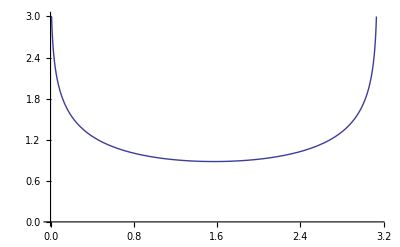

```mathematica
Plot[Log[(1+2 Cos[θ/2]+Cos[θ]) Csc[θ]^2 (1-Cos[θ]+2 Sin[θ/2])]/2,{θ,0,π},PlotRange->{{0,π},{0,3}}]
```

```mathematica
(*For a line passing through a circle approaching the origin at minimum distance d*)
ψ=ArcTan[d/z]-θ;
R0=Sqrt[z^2+d^2];
r=Sqrt[RE^2+R0^2-2RE R0 Cos[ψ]]
```

```mathematica
Assuming[RE>d>0&&-RE<z<RE&&0<θ<2π,FullSimplify[√(d^2+RE^2+z^2-2 RE √(d^2+z^2) Cos[θ-ArcTan[d/z]])]]
```

√(d^2+RE^2+z^2-(2 RE (z Cos[θ]+d Sin[θ]))/Sign[z])

```mathematica
Assuming[RE>d>0&&-RE<z<RE&&0<θ<2π,Integrate[Energy/(2RE Sqrt[d^2+RE^2-2 RE d Sin[θ]+z^2-2RE z Cos[θ]]),{z,-RE,RE}]]
```

ConditionalExpression[1/(2 RE)Energy (-Log[-RE Cos[θ]+√(d^2+RE^2-2 d RE Sin[θ])]-Log[RE Cos[θ]+√(d^2+RE^2-2 d RE Sin[θ])]+Log[RE-RE Cos[θ]+√(d^2+2 RE^2-2 RE^2 Cos[θ]-2 d RE Sin[θ])]+Log[RE+RE Cos[θ]+√(d^2+2 RE^2+2 RE^2 Cos[θ]-2 d RE Sin[θ])]),d≠RE Sin[θ]&&d^2+2 RE^2≥2 RE (RE Cos[θ]+d Sin[θ])&&d^2+2 RE^2+2 RE^2 Cos[θ]≥2 d RE Sin[θ]&&(-π+θ)/(2 π)∉Integers]

```mathematica
RE=1
Energy=1
```

1

1

```mathematica
Manipulate[Plot[1/(2 RE)Energy (-Log[-RE Cos[θ]+√(d^2+RE^2-2 d RE Sin[θ])]-Log[RE Cos[θ]+√(d^2+RE^2-2 d RE Sin[θ])]+Log[RE-RE Cos[θ]+√(d^2+2 RE^2-2 RE^2 Cos[θ]-2 d RE Sin[θ])]+Log[RE+RE Cos[θ]+√(d^2+2 RE^2+2 RE^2 Cos[θ]-2 d RE Sin[θ])]),{θ,0,2π},PlotRange->{{0,2π},{0,2π}}],{d,-1,1}]
```

```mathematica
(*Now we consider the case of a 2-D core*)
r1=Sqrt[z^2+RC^2-2z RC Cos[θ1]];
r2=Sqrt[RE^2+RC^2-2RE RC Cos[θ-θ1]];
Assuming[RE>RC>0&&0<r1<RE&&0<r2<RE&&0<θ1<θ<π,Solve[(r1 RE)/(z Sin[θ1])==r2/(Sin[θ]Cos[θ1]-Cos[θ]Sin[θ1]),θ1]]
```

{{Sin[θ]→(RC (RE Sin[θ-θ1]+z Sin[θ1]))/(RE z)},{z→0,RE→0},{Sin[θ]→((RC^2 z^2+RE^2 z^2-RC^2 RE^2 Cos[θ]^2-RE^2 z^2 Cos[θ]^2) Csc[θ1])/(2 RC RE z^2),Cos[θ1]→0},{Sin[θ1]→0,RE→0},{Sin[θ1]→0,Cos[θ1]→0},{Cos[θ]→-1,Cos[θ1]→0,RC→0},{Cos[θ]→0,z→0,Cos[θ1]→0},{Cos[θ]→1,Cos[θ1]→0,RC→0},{Sin[θ1]→0,z→0,Cos[θ1]→0},{Sin[θ1]→0,Cos[θ1]→0,RC→0}}